# HornSchunck

## Start

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
packageDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalCyclope1D`"
```

```mathematica
noteBookMode="HornSchunck";
```

## Test Points {line1, line2, pyrf12}

```mathematica
dis=1;
```

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-dis,30-dis}],1];

line1=GaussianFilter[Table[p,{p,1,30}],1];
line2=GaussianFilter[Table[p,{p,1-dis,30-dis}],1];

ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

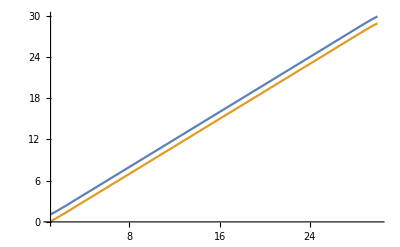

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,4];
pyrf2=pyrFuncGen[line2,4];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[1,1,1]][x],pyrf12[[1,2,1]][x]},{x,1,30}]
```

```mathematica
flowHornSchunck[i_,length_,{{f1_,f1x_},{f2_,f2x_}},lamda_]:=Block[{u,u1,mask,fx,ft,uav,p,d},(

(*We define fx*)
fx[x_]:=0.5*(f1x[x]+f2x[x]);

(*We define ft*)
ft[x_]:=f2[x]-f1[x];

mask={1,-2,1};
u=Table[0.,{k,length}];
u1=Table[0.,{k,length}];

Do[
Do[

uav=Mean[u[[x-1;;x+1]]*mask];
p=fx[x]*uav+ft[x];
d=lamda+fx[x]^2 ;
u1[[x]]=uav-fx[x]*p/d;
,{x,Range[2,length-1]}];

u=u1;
,{k,i}];

u
)]
```

```mathematica
flowHornSchunck[10,30,pyrf12[[1]],1]
```

{0.,0.434838,0.491912,0.498827,0.499947,0.499945,0.500011,0.499996,0.500001,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.500001,0.499996,0.500011,0.499945,0.499947,0.498827,0.491912,0.434838,0.}